## Tutorial for CircuitModeler

It is advised that you turn on “Show open/close icon for cell groups” in Mathematica’s preferences under the Interface tab. This will put little arrows next to the sections below to make them easier to open and close.

### Preamble

First, import the circuit-modeler library:

```mathematica
Needs["CircuitModeler`"]
```

## Inline Documentation

Any symbol publicly defined in CircuitModeler comes with terse inline documentation usage strings, just like functions built-in to Mathematica. These documentation strings can be accessed by prepending a question mark to the symbol and running the cell. For example,

```mathematica
?ScatteringParameters
```

ScatteringParameters[circuit_Circuit,ports,Z0,s] finds the scattering parameters of the given linear circuit assuming that the impedance, Z0, is the same for all ports. As a usage note, *don't* include the impedances or sources in the input circuit. The input ports should be a list of tuples specifying the nodes you want to use for a given port.

## Creating Circuits and Visualizing Them

### Components and Nodes

There are four built-in circuit element types:

```mathematica
Resistor
Capacitor
Inductor
Source
```

For a given circuit element, 3 or 4 arguments are needed to define it. 
 ⁃ The first two specify which nodes the circuit is connected to. 
 ⁃ The third gives a unique name to the circuit element.
 ⁃ For elements with a value, the fourth argument gives the value of the element (ex. resistance), and can be symbolic.

For example, here is a resistor named $R with resistance R connected to node 1 on one end, and node 2 on the other end.

```mathematica
Resistor[1,2,$R,R]
```

The dollar signs are not necessary, they are just used by convention in this tutorial to differentiate component names from their values.
A node can be any undefined symbol or number. This means they can be given readable names: (note C1 is used because C is a protected symbol in Mathematica. A number of sigle letter capital symbols are protected, like D and N)

```mathematica
Capacitor[$in,$gnd,$C,C1]
```

The source element type is used to denote a voltage or current source, and does not accept a value argument:

```mathematica
Source[1,2,$S]
```

### Circuits

Circuits are formed by connecting nodes together with various circuit elements. These elements are wrapped together with the Circuit head. For example, two resistors in parallel, and two resistors in series:

```mathematica
parallelResistors=Circuit[Resistor[1,2,$R1,R1],Resistor[1,2,$R2,R2]];
seriesResistors=Circuit[Resistor[1,2,$R1,R1],Resistor[2,3,$R2,R2]];
```

Or, here are parallel and series RLC circuits:

```mathematica
parallelRLC=Circuit[
Source[1,$gnd,$S],
Resistor[1,$gnd,$R,R],
Inductor[1,$gnd,$L,L],
Capacitor[1,$gnd,$C,C1]
];
seriesRLC=Circuit[
Source[1,$gnd,$S],
Resistor[1,2,$R,R],
Inductor[2,3,$L,L],
Capacitor[3,$gnd,$C,C1]
];
```

### Visualizing Circuits

We can visualize circuits with the CircuitGraph function. Mathematica’s graph plotting function doesn’t always lay a circuit out in the most intuitive way, but it is way easier to look at then the raw code.

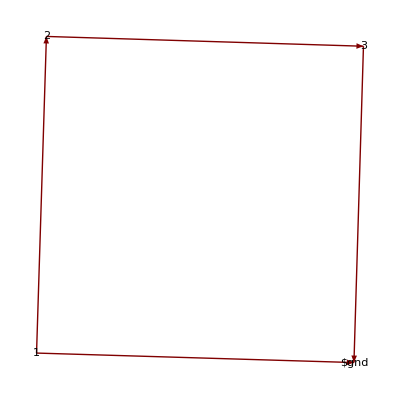
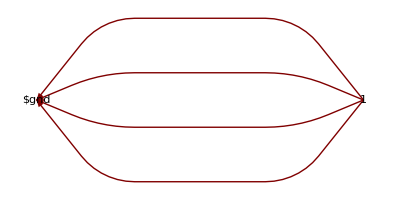

```mathematica
{CircuitGraph[seriesRLC],CircuitGraph[parallelRLC]}
```

## Circuit Equations

### Kirchhoff’s Laws

```mathematica
?KirchhoffsLaws
```

KirchhoffsLaws[circuit_Circuit, i_Symbol, v_Symbol] returns {voltageEquations, currentEquations} where voltageEquations and currentEquations are lists of equations that the voltages, v, and the currents, i, have to satisfy according to Kirchhoff's two circuit laws.

The function KirchhoffsLaws[circuit,i,v] applies Kirchhoff’s current law to every node of the circuit graph, and applies Kirchoff’s voltage law to every closed loop of the graph and returns a set of equations for each. The inputs i and v tell the function what symbols to use to represent voltage and current.

```mathematica
KirchhoffsLaws[parallelRLC,i,v]
KirchhoffsLaws[seriesRLC,i,v]
```

{{i_($C)==-i_($L)-i_($R)-i_($S)},{v_($R)==v_($S),v_($L)==v_($S),v_($C)==v_($S)}}

{{i_($R)==-i_($S),i_($L)==-i_($S),i_($C)==-i_($S)},{v_($C)==-v_($L)-v_($R)+v_($S)}}

### Circuit Equation

The function CircuitEquation[circuit,termsOfInterest,i,v,t,order] attempted to find a set of equations in the time domain which involve only the terms of interest. i and v are the symbols for current and voltage, t is the symbol for time, and order is a nuisance argument which should be set to an integer specifying how many times to differentiate all of the starting 
equations before trying to reduce. For a resistor network, this is 0, for an RLC circuit, this is 1, for an RLC with matching capatitor, it is 2, etc.

Terms are entered in the format, for example, i[$L,2,t] which refers to the second derivative of the current through component $L.

Note that it may not be possible to solve for the desired terms, in which case, some other terms will probably be in there. Choosing the order parameter and the terms of interest involves some intuition about your circuit.

In the following example, we get a set of equations that depend only on the derivative of the inductor’s current, the voltage of the source, and the current through the capacitor.

```mathematica
CircuitEquation[parallelRLC, {i[$L,1,t],i[$S,0,t],i[$C,0,t]}, i, v, t, 1]
```

{R i[$C,0,t]+R i[$L,0,t]+L i[$L,1,t]+R i[$S,0,t]==0}

### Laplace Circuit Equation

The function LaplaceCircuitEquation[circuit,solveFor,inTermsOf,i,v,s] is the Laplace domain analog of the function CircuitEquation in the previous section. Since moving to the Laplace domain reduces solving DE’s to solving algebra (which is easier for Mathematica), this function is somewhat more robust than CircuitEquation.
The argument solveFor is a current or voltage across an element (or list of), and inTermsOf is a current or voltage across an element (or list of). s is the Laplace domain symbol conjugate to time.

For example, consider the following matched RLC circuit with a source in series with a resistive impedance Rs:

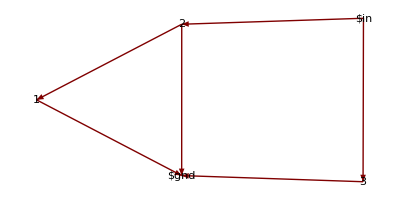

```mathematica
matchedRLC=Circuit[
Capacitor[$in,2,$Cm,Cm],
Capacitor[2,$gnd,$Ct,Ct],
Inductor[2,1,$L,L],
Resistor[1,$gnd,$R,R],
Resistor[3,$gnd,$Rs,Rs],
Source[$in,3,$source]
];
CircuitGraph[matchedRLC]
```

In the following, we solve for the current through the inductor as a function of the voltage across the source. This effectively gives the transfer function between the two elements.

```mathematica
LaplaceCircuitEquation[Join[circuit,Circuit[Resistor[3,$gnd,$Rs,Rs],Source[$in,3,$source]]],i[$L,s],v[$source,s],i,v,s]
```

{i[$L,s]→v[$source,s]/(R+(Ct R)/Cm+Rs+1/(Cm s)+L s+(Ct L s)/Cm+Ct R Rs s+Ct L Rs s^2)}

## Scattering Parameters

We can use ScatteringParameters[circuit,ports,Z0,s] to compute the S parameter matrix of a circuit over an arbitrary number of ports. Here, ports is a list ports={{node11,node12},{node21,node22},...,{nodeN1,nodeN2}} is a list of ports to do the calculation for, Z0 is the reference impedance of each port, and s is the Laplace domain independent variable.
The j’th column of the scattering matrix is computed by attaching a Source to the j’th port and Resistors of value Z0 to all of the other ports of the circuit. Then the voltages and currents through ports i and j are solved for using LaplaceCircuitEquation in terms of the current through port j. S_ij is computed using (V_i+Z_0 I_i)/(V_j-Z_0 I_j). Since each V_i, I_i, V_j, I_j are linear functions of I_j, this variable cancels out in the division and the quantity of interest remains.

Note that because of the way this function works, as described above, the sources and reference impedance should not be included in the input circuit.

#### Example: 1-port Capacitor

Compute the 1×1 scattering matrix of a capacitor of capacitance c.

```mathematica
ScatteringParameters[
Circuit[Capacitor[$in,$out,$C,c]],
{{$in,$out}},Z0,s
]//MatrixForm
```

((1-c s Z0)/(1+c s Z0))

#### Example: 2-port Capacitor

Compute the 2×2 scattering matrix of a shunting resistor of resistance R.

```mathematica
ScatteringParameters[
Circuit[Resistor[$in,$out,$R,R]],
{{$in,$out},{$in,$out}},Z0,s
]//MatrixForm
```

(-Z0/(2 R+Z0) | (2 R)/(2 R+Z0)
(2 R)/(2 R+Z0) | -Z0/(2 R+Z0))

#### Example: Matched RLC single port resonator.

```mathematica
S=ScatteringParameters[
matchedRLC=Circuit[
Capacitor[$in,2,$Cm,Cm],
Capacitor[2,$gnd,$C,Ct],
Inductor[2,1,$L,L],
Resistor[1,$gnd,$R,R]
],
{{$in,$gnd}},Rs,s
];
S//MatrixForm
```

((1+Ct s (R+L s)-Cm s (Rs-L s+Ct L Rs s^2+R (-1+Ct Rs s)))/(1+Ct s (R+L s)+Cm s (R+Rs+L s+Ct R Rs s+Ct L Rs s^2)))

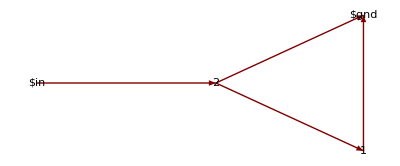

```mathematica
CircuitGraph[matchedRLC]
```

We can plot the S parameters with the function SParamsPlot.

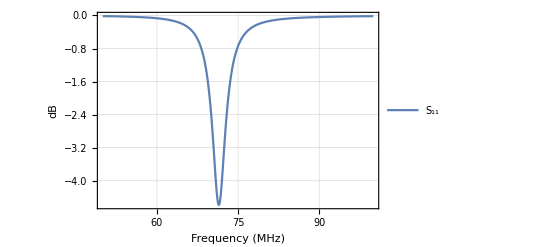

```mathematica
(*Use units where 1pF=1nH=10^6 so that MHz is the natural unit, and quantities aren't so crazy small or big.*)
pF=10^6;nH=10^6;Ω=1;
params={Cm->10 10^-12 pF,Ct->40 10^-12 pF,L->100 10^-9 nH,R->0.5Ω ,Rs->50Ω};
SParamsPlot[S,params,s,{50,100}, 20Log10[Abs[#]]&,False,PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Frequency (MHz)","dB"}]
```